```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

Read in mat file

```mathematica
Import["Sophie_Face_Ref.txt","Elements"]
```

{Data,Lines,Plaintext,String,Summary,Words}

The original meshes

```mathematica
Face=Import["Sophie_Face_Ref.txt","Data"]+1;
```

```mathematica
VerticeRef=Import["Sophie_Node_Ref.txt","Data"];
```

```mathematica
Dimensions[Face]
```

{7942,3}

```mathematica
Dimensions[VerticeRef]
```

{4084,3}

The parameterization results

```mathematica
UV=Import["Sophie_UV.txt","Data"];
```

The principal directions and curvatures of the reference surface

```mathematica
PD1Ref=Import["Sophie_PD1_Ref.txt","Data"];
PD2Ref=Import["Sophie_PD2_Ref.txt","Data"];
k1Ref=Flatten[Import["Sophie_k1_Ref.txt","Data"]];
k2Ref=Flatten[Import["Sophie_k2_Ref.txt","Data"]];
```

```mathematica
Dimensions[k1Ref]
```

{4084}

```mathematica
nNodes=Dimensions[VerticeRef][[1]]
nFaces=Dimensions[Face][[1]]
```

4084

7942

```mathematica
Table[{{VerticeRef[[Face[[n,1]],1]],VerticeRef[[Face[[n,1]],2]],VerticeRef[[Face[[n,1]],3]]},{VerticeRef[[Face[[n,2]],1]],VerticeRef[[Face[[n,2]],2]],VerticeRef[[Face[[n,2]],3]]},{VerticeRef[[Face[[n,3]],1]],VerticeRef[[Face[[n,3]],2]],VerticeRef[[Face[[n,3]],3]]}},{n,1,nFaces}];
ModelRef=Graphics3D[{Polygon[%],PerformanceGoal->"Quality",MaxRecursion->10},Boxed->False]
```

-Graphics3D-

调整UV平面

```mathematica
(*旋转角度（以弧度为单位）*)
angle=195 Pi/180; (*这里设置为45度，你可以根据需要修改*)
(*创建旋转变换函数*)
rotationTransform=RotationTransform[angle];
(*对所有节点进行旋转操作*)
rotatedNodes=rotationTransform/@UV;
```

```mathematica
Table[{{-rotatedNodes[[Face[[n,1]],1]],rotatedNodes[[Face[[n,1]],2]],0},{-rotatedNodes[[Face[[n,2]],1]],rotatedNodes[[Face[[n,2]],2]],0},{-rotatedNodes[[Face[[n,3]],1]],rotatedNodes[[Face[[n,3]],2]],0}},{n,1,nFaces}];
Graphics3D[{Polygon[%],PerformanceGoal->"Quality",MaxRecursion->10},Boxed->False]
```

-Graphics3D-

```mathematica
UV=Table[{-rotatedNodes[[n,1]],rotatedNodes[[n,2]]},{n,1,nNodes}]//N
```

```mathematica
Table[{{UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],0},{UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],0},{UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],0}},{n,1,nFaces}];
UVPlane=Graphics3D[{Polygon[%],PerformanceGoal->"Quality",MaxRecursion->10},Boxed->False]
```

-Graphics3D-

```mathematica
Show[ModelRef,UVPlane]
```

-Graphics3D-

检查一下由Libigl计算的UV平面圆有多大

```mathematica
Max[UV[[All,1]]]-Min[UV[[All,1]]]
```

1.99988

```mathematica
Max[UV[[All,2]]]-Min[UV[[All,2]]]
```

1.99985

是一个半径几乎为1的圆

接下来要在半径几乎为1的圆上生成规则的网格，标准化的网格

计算混合积

```mathematica
MixProd=Table[({UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],1.0}).({UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],1.0}×{UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],1.0}),{n,1,nFaces}];
```

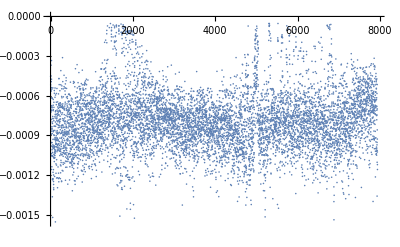

```mathematica
ListPlot[MixProd,PlotRange->All]
```

```mathematica
ii=1;Tabii={};While[ii≤ nFaces,If[MixProd[[ii]]< 0,AppendTo[Tabii,ii]];ii++];
```

```mathematica
Tabii
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,704,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989,990,991,992,993,994,995,996,997,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1008,1009,1010,1011,1012,1013,1014,1015,1016,1017,1018,1019,1020,1021,1022,1023,1024,1025,1026,1027,1028,1029,1030,1031,1032,1033,1034,1035,1036,1037,1038,1039,1040,1041,1042,1043,1044,1045,1046,1047,1048,1049,1050,1051,1052,1053,1054,1055,1056,1057,1058,1059,1060,1061,1062,1063,1064,1065,1066,1067,1068,1069,1070,1071,1072,1073,1074,1075,1076,1077,1078,1079,1080,1081,1082,1083,1084,1085,1086,1087,1088,1089,1090,1091,1092,1093,1094,1095,1096,1097,1098,1099,1100,1101,1102,1103,1104,1105,1106,1107,1108,1109,1110,1111,1112,1113,1114,1115,1116,1117,1118,1119,1120,1121,1122,1123,1124,1125,1126,1127,1128,1129,1130,1131,1132,1133,1134,1135,1136,1137,1138,1139,1140,1141,1142,1143,1144,1145,1146,1147,1148,1149,1150,1151,1152,1153,1154,1155,1156,1157,1158,1159,1160,1161,1162,1163,1164,1165,1166,1167,1168,1169,1170,1171,1172,1173,1174,1175,1176,1177,1178,1179,1180,1181,1182,1183,1184,1185,1186,1187,1188,1189,1190,1191,1192,1193,1194,1195,1196,1197,1198,1199,1200,1201,1202,1203,1204,1205,1206,1207,1208,1209,1210,1211,1212,1213,1214,1215,1216,1217,1218,1219,1220,1221,1222,1223,1224,1225,1226,1227,1228,1229,1230,1231,1232,1233,1234,1235,1236,1237,1238,1239,1240,1241,1242,1243,1244,1245,1246,1247,1248,1249,1250,1251,1252,1253,1254,1255,1256,1257,1258,1259,1260,1261,1262,1263,1264,1265,1266,1267,1268,1269,1270,1271,1272,1273,1274,1275,1276,1277,1278,1279,1280,1281,1282,1283,1284,1285,1286,1287,1288,1289,1290,1291,1292,1293,1294,1295,1296,1297,1298,1299,1300,1301,1302,1303,1304,1305,1306,1307,1308,1309,1310,1311,1312,1313,1314,1315,1316,1317,1318,1319,1320,1321,1322,1323,1324,1325,1326,1327,1328,1329,1330,1331,1332,1333,1334,1335,1336,1337,1338,1339,1340,1341,1342,1343,1344,1345,1346,1347,1348,1349,1350,1351,1352,1353,1354,1355,1356,1357,1358,1359,1360,1361,1362,1363,1364,1365,1366,1367,1368,1369,1370,1371,1372,1373,1374,1375,1376,1377,1378,1379,1380,1381,1382,1383,1384,1385,1386,1387,1388,1389,1390,1391,1392,1393,1394,1395,1396,1397,1398,1399,1400,1401,1402,1403,1404,1405,1406,1407,1408,1409,1410,1411,1412,1413,1414,1415,1416,1417,1418,1419,1420,1421,1422,1423,1424,1425,1426,1427,1428,1429,1430,1431,1432,1433,1434,1435,1436,1437,1438,1439,1440,1441,1442,1443,1444,1445,1446,1447,1448,1449,1450,1451,1452,1453,1454,1455,1456,1457,1458,1459,1460,1461,1462,1463,1464,1465,1466,1467,1468,1469,1470,1471,1472,1473,1474,1475,1476,1477,1478,1479,1480,1481,1482,1483,1484,1485,1486,1487,1488,1489,1490,1491,1492,1493,1494,1495,1496,1497,1498,1499,1500,1501,1502,1503,1504,1505,1506,1507,1508,1509,1510,1511,1512,1513,1514,1515,1516,1517,1518,1519,1520,1521,1522,1523,1524,1525,1526,1527,1528,1529,1530,1531,1532,1533,1534,1535,1536,1537,1538,1539,1540,1541,1542,1543,1544,1545,1546,1547,1548,1549,1550,1551,1552,1553,1554,1555,1556,1557,1558,1559,1560,1561,1562,1563,1564,1565,1566,1567,1568,1569,1570,1571,1572,1573,1574,1575,1576,1577,1578,1579,1580,1581,1582,1583,1584,1585,1586,1587,1588,1589,1590,1591,1592,1593,1594,1595,1596,1597,1598,1599,1600,1601,1602,1603,1604,1605,1606,1607,1608,1609,1610,1611,1612,1613,1614,1615,1616,1617,1618,1619,1620,1621,1622,1623,1624,1625,1626,1627,1628,1629,1630,1631,1632,1633,1634,1635,1636,1637,1638,1639,1640,1641,1642,1643,1644,1645,1646,1647,1648,1649,1650,1651,1652,1653,1654,1655,1656,1657,1658,1659,1660,1661,1662,1663,1664,1665,1666,1667,1668,1669,1670,1671,1672,1673,1674,1675,1676,1677,1678,1679,1680,1681,1682,1683,1684,1685,1686,1687,1688,1689,1690,1691,1692,1693,1694,1695,1696,1697,1698,1699,1700,1701,1702,1703,1704,1705,1706,1707,1708,1709,1710,1711,1712,1713,1714,1715,1716,1717,1718,1719,1720,1721,1722,1723,1724,1725,1726,1727,1728,1729,1730,1731,1732,1733,1734,1735,1736,1737,1738,1739,1740,1741,1742,1743,1744,1745,1746,1747,1748,1749,1750,1751,1752,1753,1754,1755,1756,1757,1758,1759,1760,1761,1762,1763,1764,1765,1766,1767,1768,1769,1770,1771,1772,1773,1774,1775,1776,1777,1778,1779,1780,1781,1782,1783,1784,1785,1786,1787,1788,1789,1790,1791,1792,1793,1794,1795,1796,1797,1798,1799,1800,1801,1802,1803,1804,1805,1806,1807,1808,1809,1810,1811,1812,1813,1814,1815,1816,1817,1818,1819,1820,1821,1822,1823,1824,1825,1826,1827,1828,1829,1830,1831,1832,1833,1834,1835,1836,1837,1838,1839,1840,1841,1842,1843,1844,1845,1846,1847,1848,1849,1850,1851,1852,1853,1854,1855,1856,1857,1858,1859,1860,1861,1862,1863,1864,1865,1866,1867,1868,1869,1870,1871,1872,1873,1874,1875,1876,1877,1878,1879,1880,1881,1882,1883,1884,1885,1886,1887,1888,1889,1890,1891,1892,1893,1894,1895,1896,1897,1898,1899,1900,1901,1902,1903,1904,1905,1906,1907,1908,1909,1910,1911,1912,1913,1914,1915,1916,1917,1918,1919,1920,1921,1922,1923,1924,1925,1926,1927,1928,1929,1930,1931,1932,1933,1934,1935,1936,1937,1938,1939,1940,1941,1942,1943,1944,1945,1946,1947,1948,1949,1950,1951,1952,1953,1954,1955,1956,1957,1958,1959,1960,1961,1962,1963,1964,1965,1966,1967,1968,1969,1970,1971,1972,1973,1974,1975,1976,1977,1978,1979,1980,1981,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022,2023,2024,2025,2026,2027,2028,2029,2030,2031,2032,2033,2034,2035,2036,2037,2038,2039,2040,2041,2042,2043,2044,2045,2046,2047,2048,2049,2050,2051,2052,2053,2054,2055,2056,2057,2058,2059,2060,2061,2062,2063,2064,2065,2066,2067,2068,2069,2070,2071,2072,2073,2074,2075,2076,2077,2078,2079,2080,2081,2082,2083,2084,2085,2086,2087,2088,2089,2090,2091,2092,2093,2094,2095,2096,2097,2098,2099,2100,2101,2102,2103,2104,2105,2106,2107,2108,2109,2110,2111,2112,2113,2114,2115,2116,2117,2118,2119,2120,2121,2122,2123,2124,2125,2126,2127,2128,2129,2130,2131,2132,2133,2134,2135,2136,2137,2138,2139,2140,2141,2142,2143,2144,2145,2146,2147,2148,2149,2150,2151,2152,2153,2154,2155,2156,2157,2158,2159,2160,2161,2162,2163,2164,2165,2166,2167,2168,2169,2170,2171,2172,2173,2174,2175,2176,2177,2178,2179,2180,2181,2182,2183,2184,2185,2186,2187,2188,2189,2190,2191,2192,2193,2194,2195,2196,2197,2198,2199,2200,2201,2202,2203,2204,2205,2206,2207,2208,2209,2210,2211,2212,2213,2214,2215,2216,2217,2218,2219,2220,2221,2222,2223,2224,2225,2226,2227,2228,2229,2230,2231,2232,2233,2234,2235,2236,2237,2238,2239,2240,2241,2242,2243,2244,2245,2246,2247,2248,2249,2250,2251,2252,2253,2254,2255,2256,2257,2258,2259,2260,2261,2262,2263,2264,2265,2266,2267,2268,2269,2270,2271,2272,2273,2274,2275,2276,2277,2278,2279,2280,2281,2282,2283,2284,2285,2286,2287,2288,2289,2290,2291,2292,2293,2294,2295,2296,2297,2298,2299,2300,2301,2302,2303,2304,2305,2306,2307,2308,2309,2310,2311,2312,2313,2314,2315,2316,2317,2318,2319,2320,2321,2322,2323,2324,2325,2326,2327,2328,2329,2330,2331,2332,2333,2334,2335,2336,2337,2338,2339,2340,2341,2342,2343,2344,2345,2346,2347,2348,2349,2350,2351,2352,2353,2354,2355,2356,2357,2358,2359,2360,2361,2362,2363,2364,2365,2366,2367,2368,2369,2370,2371,2372,2373,2374,2375,2376,2377,2378,2379,2380,2381,2382,2383,2384,2385,2386,2387,2388,2389,2390,2391,2392,2393,2394,2395,2396,2397,2398,2399,2400,2401,2402,2403,2404,2405,2406,2407,2408,2409,2410,2411,2412,2413,2414,2415,2416,2417,2418,2419,2420,2421,2422,2423,2424,2425,2426,2427,2428,2429,2430,2431,2432,2433,2434,2435,2436,2437,2438,2439,2440,2441,2442,2443,2444,2445,2446,2447,2448,2449,2450,2451,2452,2453,2454,2455,2456,2457,2458,2459,2460,2461,2462,2463,2464,2465,2466,2467,2468,2469,2470,2471,2472,2473,2474,2475,2476,2477,2478,2479,2480,2481,2482,2483,2484,2485,2486,2487,2488,2489,2490,2491,2492,2493,2494,2495,2496,2497,2498,2499,2500,2501,2502,2503,2504,2505,2506,2507,2508,2509,2510,2511,2512,2513,2514,2515,2516,2517,2518,2519,2520,2521,2522,2523,2524,2525,2526,2527,2528,2529,2530,2531,2532,2533,2534,2535,2536,2537,2538,2539,2540,2541,2542,2543,2544,2545,2546,2547,2548,2549,2550,2551,2552,2553,2554,2555,2556,2557,2558,2559,2560,2561,2562,2563,2564,2565,2566,2567,2568,2569,2570,2571,2572,2573,2574,2575,2576,2577,2578,2579,2580,2581,2582,2583,2584,2585,2586,2587,2588,2589,2590,2591,2592,2593,2594,2595,2596,2597,2598,2599,2600,2601,2602,2603,2604,2605,2606,2607,2608,2609,2610,2611,2612,2613,2614,2615,2616,2617,2618,2619,2620,2621,2622,2623,2624,2625,2626,2627,2628,2629,2630,2631,2632,2633,2634,2635,2636,2637,2638,2639,2640,2641,2642,2643,2644,2645,2646,2647,2648,2649,2650,2651,2652,2653,2654,2655,2656,2657,2658,2659,2660,2661,2662,2663,2664,2665,2666,2667,2668,2669,2670,2671,2672,2673,2674,2675,2676,2677,2678,2679,2680,2681,2682,2683,2684,2685,2686,2687,2688,2689,2690,2691,2692,2693,2694,2695,2696,2697,2698,2699,2700,2701,2702,2703,2704,2705,2706,2707,2708,2709,2710,2711,2712,2713,2714,2715,2716,2717,2718,2719,2720,2721,2722,2723,2724,2725,2726,2727,2728,2729,2730,2731,2732,2733,2734,2735,2736,2737,2738,2739,2740,2741,2742,2743,2744,2745,2746,2747,2748,2749,2750,2751,2752,2753,2754,2755,2756,2757,2758,2759,2760,2761,2762,2763,2764,2765,2766,2767,2768,2769,2770,2771,2772,2773,2774,2775,2776,2777,2778,2779,2780,2781,2782,2783,2784,2785,2786,2787,2788,2789,2790,2791,2792,2793,2794,2795,2796,2797,2798,2799,2800,2801,2802,2803,2804,2805,2806,2807,2808,2809,2810,2811,2812,2813,2814,2815,2816,2817,2818,2819,2820,2821,2822,2823,2824,2825,2826,2827,2828,2829,2830,2831,2832,2833,2834,2835,2836,2837,2838,2839,2840,2841,2842,2843,2844,2845,2846,2847,2848,2849,2850,2851,2852,2853,2854,2855,2856,2857,2858,2859,2860,2861,2862,2863,2864,2865,2866,2867,2868,2869,2870,2871,2872,2873,2874,2875,2876,2877,2878,2879,2880,2881,2882,2883,2884,2885,2886,2887,2888,2889,2890,2891,2892,2893,2894,2895,2896,2897,2898,2899,2900,2901,2902,2903,2904,2905,2906,2907,2908,2909,2910,2911,2912,2913,2914,2915,2916,2917,2918,2919,2920,2921,2922,2923,2924,2925,2926,2927,2928,2929,2930,2931,2932,2933,2934,2935,2936,2937,2938,2939,2940,2941,2942,2943,2944,2945,2946,2947,2948,2949,2950,2951,2952,2953,2954,2955,2956,2957,2958,2959,2960,2961,2962,2963,2964,2965,2966,2967,2968,2969,2970,2971,2972,2973,2974,2975,2976,2977,2978,2979,2980,2981,2982,2983,2984,2985,2986,2987,2988,2989,2990,2991,2992,2993,2994,2995,2996,2997,2998,2999,3000,3001,3002,3003,3004,3005,3006,3007,3008,3009,3010,3011,3012,3013,3014,3015,3016,3017,3018,3019,3020,3021,3022,3023,3024,3025,3026,3027,3028,3029,3030,3031,3032,3033,3034,3035,3036,3037,3038,3039,3040,3041,3042,3043,3044,3045,3046,3047,3048,3049,3050,3051,3052,3053,3054,3055,3056,3057,3058,3059,3060,3061,3062,3063,3064,3065,3066,3067,3068,3069,3070,3071,3072,3073,3074,3075,3076,3077,3078,3079,3080,3081,3082,3083,3084,3085,3086,3087,3088,3089,3090,3091,3092,3093,3094,3095,3096,3097,3098,3099,3100,3101,3102,3103,3104,3105,3106,3107,3108,3109,3110,3111,3112,3113,3114,3115,3116,3117,3118,3119,3120,3121,3122,3123,3124,3125,3126,3127,3128,3129,3130,3131,3132,3133,3134,3135,3136,3137,3138,3139,3140,3141,3142,3143,3144,3145,3146,3147,3148,3149,3150,3151,3152,3153,3154,3155,3156,3157,3158,3159,3160,3161,3162,3163,3164,3165,3166,3167,3168,3169,3170,3171,3172,3173,3174,3175,3176,3177,3178,3179,3180,3181,3182,3183,3184,3185,3186,3187,3188,3189,3190,3191,3192,3193,3194,3195,3196,3197,3198,3199,3200,3201,3202,3203,3204,3205,3206,3207,3208,3209,3210,3211,3212,3213,3214,3215,3216,3217,3218,3219,3220,3221,3222,3223,3224,3225,3226,3227,3228,3229,3230,3231,3232,3233,3234,3235,3236,3237,3238,3239,3240,3241,3242,3243,3244,3245,3246,3247,3248,3249,3250,3251,3252,3253,3254,3255,3256,3257,3258,3259,3260,3261,3262,3263,3264,3265,3266,3267,3268,3269,3270,3271,3272,3273,3274,3275,3276,3277,3278,3279,3280,3281,3282,3283,3284,3285,3286,3287,3288,3289,3290,3291,3292,3293,3294,3295,3296,3297,3298,3299,3300,3301,3302,3303,3304,3305,3306,3307,3308,3309,3310,3311,3312,3313,3314,3315,3316,3317,3318,3319,3320,3321,3322,3323,3324,3325,3326,3327,3328,3329,3330,3331,3332,3333,3334,3335,3336,3337,3338,3339,3340,3341,3342,3343,3344,3345,3346,3347,3348,3349,3350,3351,3352,3353,3354,3355,3356,3357,3358,3359,3360,3361,3362,3363,3364,3365,3366,3367,3368,3369,3370,3371,3372,3373,3374,3375,3376,3377,3378,3379,3380,3381,3382,3383,3384,3385,3386,3387,3388,3389,3390,3391,3392,3393,3394,3395,3396,3397,3398,3399,3400,3401,3402,3403,3404,3405,3406,3407,3408,3409,3410,3411,3412,3413,3414,3415,3416,3417,3418,3419,3420,3421,3422,3423,3424,3425,3426,3427,3428,3429,3430,3431,3432,3433,3434,3435,3436,3437,3438,3439,3440,3441,3442,3443,3444,3445,3446,3447,3448,3449,3450,3451,3452,3453,3454,3455,3456,3457,3458,3459,3460,3461,3462,3463,3464,3465,3466,3467,3468,3469,3470,3471,3472,3473,3474,3475,3476,3477,3478,3479,3480,3481,3482,3483,3484,3485,3486,3487,3488,3489,3490,3491,3492,3493,3494,3495,3496,3497,3498,3499,3500,3501,3502,3503,3504,3505,3506,3507,3508,3509,3510,3511,3512,3513,3514,3515,3516,3517,3518,3519,3520,3521,3522,3523,3524,3525,3526,3527,3528,3529,3530,3531,3532,3533,3534,3535,3536,3537,3538,3539,3540,3541,3542,3543,3544,3545,3546,3547,3548,3549,3550,3551,3552,3553,3554,3555,3556,3557,3558,3559,3560,3561,3562,3563,3564,3565,3566,3567,3568,3569,3570,3571,3572,3573,3574,3575,3576,3577,3578,3579,3580,3581,3582,3583,3584,3585,3586,3587,3588,3589,3590,3591,3592,3593,3594,3595,3596,3597,3598,3599,3600,3601,3602,3603,3604,3605,3606,3607,3608,3609,3610,3611,3612,3613,3614,3615,3616,3617,3618,3619,3620,3621,3622,3623,3624,3625,3626,3627,3628,3629,3630,3631,3632,3633,3634,3635,3636,3637,3638,3639,3640,3641,3642,3643,3644,3645,3646,3647,3648,3649,3650,3651,3652,3653,3654,3655,3656,3657,3658,3659,3660,3661,3662,3663,3664,3665,3666,3667,3668,3669,3670,3671,3672,3673,3674,3675,3676,3677,3678,3679,3680,3681,3682,3683,3684,3685,3686,3687,3688,3689,3690,3691,3692,3693,3694,3695,3696,3697,3698,3699,3700,3701,3702,3703,3704,3705,3706,3707,3708,3709,3710,3711,3712,3713,3714,3715,3716,3717,3718,3719,3720,3721,3722,3723,3724,3725,3726,3727,3728,3729,3730,3731,3732,3733,3734,3735,3736,3737,3738,3739,3740,3741,3742,3743,3744,3745,3746,3747,3748,3749,3750,3751,3752,3753,3754,3755,3756,3757,3758,3759,3760,3761,3762,3763,3764,3765,3766,3767,3768,3769,3770,3771,3772,3773,3774,3775,3776,3777,3778,3779,3780,3781,3782,3783,3784,3785,3786,3787,3788,3789,3790,3791,3792,3793,3794,3795,3796,3797,3798,3799,3800,3801,3802,3803,3804,3805,3806,3807,3808,3809,3810,3811,3812,3813,3814,3815,3816,3817,3818,3819,3820,3821,3822,3823,3824,3825,3826,3827,3828,3829,3830,3831,3832,3833,3834,3835,3836,3837,3838,3839,3840,3841,3842,3843,3844,3845,3846,3847,3848,3849,3850,3851,3852,3853,3854,3855,3856,3857,3858,3859,3860,3861,3862,3863,3864,3865,3866,3867,3868,3869,3870,3871,3872,3873,3874,3875,3876,3877,3878,3879,3880,3881,3882,3883,3884,3885,3886,3887,3888,3889,3890,3891,3892,3893,3894,3895,3896,3897,3898,3899,3900,3901,3902,3903,3904,3905,3906,3907,3908,3909,3910,3911,3912,3913,3914,3915,3916,3917,3918,3919,3920,3921,3922,3923,3924,3925,3926,3927,3928,3929,3930,3931,3932,3933,3934,3935,3936,3937,3938,3939,3940,3941,3942,3943,3944,3945,3946,3947,3948,3949,3950,3951,3952,3953,3954,3955,3956,3957,3958,3959,3960,3961,3962,3963,3964,3965,3966,3967,3968,3969,3970,3971,3972,3973,3974,3975,3976,3977,3978,3979,3980,3981,3982,3983,3984,3985,3986,3987,3988,3989,3990,3991,3992,3993,3994,3995,3996,3997,3998,3999,4000,4001,4002,4003,4004,4005,4006,4007,4008,4009,4010,4011,4012,4013,4014,4015,4016,4017,4018,4019,4020,4021,4022,4023,4024,4025,4026,4027,4028,4029,4030,4031,4032,4033,4034,4035,4036,4037,4038,4039,4040,4041,4042,4043,4044,4045,4046,4047,4048,4049,4050,4051,4052,4053,4054,4055,4056,4057,4058,4059,4060,4061,4062,4063,4064,4065,4066,4067,4068,4069,4070,4071,4072,4073,4074,4075,4076,4077,4078,4079,4080,4081,4082,4083,4084,4085,4086,4087,4088,4089,4090,4091,4092,4093,4094,4095,4096,4097,4098,4099,4100,4101,4102,4103,4104,4105,4106,4107,4108,4109,4110,4111,4112,4113,4114,4115,4116,4117,4118,4119,4120,4121,4122,4123,4124,4125,4126,4127,4128,4129,4130,4131,4132,4133,4134,4135,4136,4137,4138,4139,4140,4141,4142,4143,4144,4145,4146,4147,4148,4149,4150,4151,4152,4153,4154,4155,4156,4157,4158,4159,4160,4161,4162,4163,4164,4165,4166,4167,4168,4169,4170,4171,4172,4173,4174,4175,4176,4177,4178,4179,4180,4181,4182,4183,4184,4185,4186,4187,4188,4189,4190,4191,4192,4193,4194,4195,4196,4197,4198,4199,4200,4201,4202,4203,4204,4205,4206,4207,4208,4209,4210,4211,4212,4213,4214,4215,4216,4217,4218,4219,4220,4221,4222,4223,4224,4225,4226,4227,4228,4229,4230,4231,4232,4233,4234,4235,4236,4237,4238,4239,4240,4241,4242,4243,4244,4245,4246,4247,4248,4249,4250,4251,4252,4253,4254,4255,4256,4257,4258,4259,4260,4261,4262,4263,4264,4265,4266,4267,4268,4269,4270,4271,4272,4273,4274,4275,4276,4277,4278,4279,4280,4281,4282,4283,4284,4285,4286,4287,4288,4289,4290,4291,4292,4293,4294,4295,4296,4297,4298,4299,4300,4301,4302,4303,4304,4305,4306,4307,4308,4309,4310,4311,4312,4313,4314,4315,4316,4317,4318,4319,4320,4321,4322,4323,4324,4325,4326,4327,4328,4329,4330,4331,4332,4333,4334,4335,4336,4337,4338,4339,4340,4341,4342,4343,4344,4345,4346,4347,4348,4349,4350,4351,4352,4353,4354,4355,4356,4357,4358,4359,4360,4361,4362,4363,4364,4365,4366,4367,4368,4369,4370,4371,4372,4373,4374,4375,4376,4377,4378,4379,4380,4381,4382,4383,4384,4385,4386,4387,4388,4389,4390,4391,4392,4393,4394,4395,4396,4397,4398,4399,4400,4401,4402,4403,4404,4405,4406,4407,4408,4409,4410,4411,4412,4413,4414,4415,4416,4417,4418,4419,4420,4421,4422,4423,4424,4425,4426,4427,4428,4429,4430,4431,4432,4433,4434,4435,4436,4437,4438,4439,4440,4441,4442,4443,4444,4445,4446,4447,4448,4449,4450,4451,4452,4453,4454,4455,4456,4457,4458,4459,4460,4461,4462,4463,4464,4465,4466,4467,4468,4469,4470,4471,4472,4473,4474,4475,4476,4477,4478,4479,4480,4481,4482,4483,4484,4485,4486,4487,4488,4489,4490,4491,4492,4493,4494,4495,4496,4497,4498,4499,4500,4501,4502,4503,4504,4505,4506,4507,4508,4509,4510,4511,4512,4513,4514,4515,4516,4517,4518,4519,4520,4521,4522,4523,4524,4525,4526,4527,4528,4529,4530,4531,4532,4533,4534,4535,4536,4537,4538,4539,4540,4541,4542,4543,4544,4545,4546,4547,4548,4549,4550,4551,4552,4553,4554,4555,4556,4557,4558,4559,4560,4561,4562,4563,4564,4565,4566,4567,4568,4569,4570,4571,4572,4573,4574,4575,4576,4577,4578,4579,4580,4581,4582,4583,4584,4585,4586,4587,4588,4589,4590,4591,4592,4593,4594,4595,4596,4597,4598,4599,4600,4601,4602,4603,4604,4605,4606,4607,4608,4609,4610,4611,4612,4613,4614,4615,4616,4617,4618,4619,4620,4621,4622,4623,4624,4625,4626,4627,4628,4629,4630,4631,4632,4633,4634,4635,4636,4637,4638,4639,4640,4641,4642,4643,4644,4645,4646,4647,4648,4649,4650,4651,4652,4653,4654,4655,4656,4657,4658,4659,4660,4661,4662,4663,4664,4665,4666,4667,4668,4669,4670,4671,4672,4673,4674,4675,4676,4677,4678,4679,4680,4681,4682,4683,4684,4685,4686,4687,4688,4689,4690,4691,4692,4693,4694,4695,4696,4697,4698,4699,4700,4701,4702,4703,4704,4705,4706,4707,4708,4709,4710,4711,4712,4713,4714,4715,4716,4717,4718,4719,4720,4721,4722,4723,4724,4725,4726,4727,4728,4729,4730,4731,4732,4733,4734,4735,4736,4737,4738,4739,4740,4741,4742,4743,4744,4745,4746,4747,4748,4749,4750,4751,4752,4753,4754,4755,4756,4757,4758,4759,4760,4761,4762,4763,4764,4765,4766,4767,4768,4769,4770,4771,4772,4773,4774,4775,4776,4777,4778,4779,4780,4781,4782,4783,4784,4785,4786,4787,4788,4789,4790,4791,4792,4793,4794,4795,4796,4797,4798,4799,4800,4801,4802,4803,4804,4805,4806,4807,4808,4809,4810,4811,4812,4813,4814,4815,4816,4817,4818,4819,4820,4821,4822,4823,4824,4825,4826,4827,4828,4829,4830,4831,4832,4833,4834,4835,4836,4837,4838,4839,4840,4841,4842,4843,4844,4845,4846,4847,4848,4849,4850,4851,4852,4853,4854,4855,4856,4857,4858,4859,4860,4861,4862,4863,4864,4865,4866,4867,4868,4869,4870,4871,4872,4873,4874,4875,4876,4877,4878,4879,4880,4881,4882,4883,4884,4885,4886,4887,4888,4889,4890,4891,4892,4893,4894,4895,4896,4897,4898,4899,4900,4901,4902,4903,4904,4905,4906,4907,4908,4909,4910,4911,4912,4913,4914,4915,4916,4917,4918,4919,4920,4921,4922,4923,4924,4925,4926,4927,4928,4929,4930,4931,4932,4933,4934,4935,4936,4937,4938,4939,4940,4941,4942,4943,4944,4945,4946,4947,4948,4949,4950,4951,4952,4953,4954,4955,4956,4957,4958,4959,4960,4961,4962,4963,4964,4965,4966,4967,4968,4969,4970,4971,4972,4973,4974,4975,4976,4977,4978,4979,4980,4981,4982,4983,4984,4985,4986,4987,4988,4989,4990,4991,4992,4993,4994,4995,4996,4997,4998,4999,5000,5001,5002,5003,5004,5005,5006,5007,5008,5009,5010,5011,5012,5013,5014,5015,5016,5017,5018,5019,5020,5021,5022,5023,5024,5025,5026,5027,5028,5029,5030,5031,5032,5033,5034,5035,5036,5037,5038,5039,5040,5041,5042,5043,5044,5045,5046,5047,5048,5049,5050,5051,5052,5053,5054,5055,5056,5057,5058,5059,5060,5061,5062,5063,5064,5065,5066,5067,5068,5069,5070,5071,5072,5073,5074,5075,5076,5077,5078,5079,5080,5081,5082,5083,5084,5085,5086,5087,5088,5089,5090,5091,5092,5093,5094,5095,5096,5097,5098,5099,5100,5101,5102,5103,5104,5105,5106,5107,5108,5109,5110,5111,5112,5113,5114,5115,5116,5117,5118,5119,5120,5121,5122,5123,5124,5125,5126,5127,5128,5129,5130,5131,5132,5133,5134,5135,5136,5137,5138,5139,5140,5141,5142,5143,5144,5145,5146,5147,5148,5149,5150,5151,5152,5153,5154,5155,5156,5157,5158,5159,5160,5161,5162,5163,5164,5165,5166,5167,5168,5169,5170,5171,5172,5173,5174,5175,5176,5177,5178,5179,5180,5181,5182,5183,5184,5185,5186,5187,5188,5189,5190,5191,5192,5193,5194,5195,5196,5197,5198,5199,5200,5201,5202,5203,5204,5205,5206,5207,5208,5209,5210,5211,5212,5213,5214,5215,5216,5217,5218,5219,5220,5221,5222,5223,5224,5225,5226,5227,5228,5229,5230,5231,5232,5233,5234,5235,5236,5237,5238,5239,5240,5241,5242,5243,5244,5245,5246,5247,5248,5249,5250,5251,5252,5253,5254,5255,5256,5257,5258,5259,5260,5261,5262,5263,5264,5265,5266,5267,5268,5269,5270,5271,5272,5273,5274,5275,5276,5277,5278,5279,5280,5281,5282,5283,5284,5285,5286,5287,5288,5289,5290,5291,5292,5293,5294,5295,5296,5297,5298,5299,5300,5301,5302,5303,5304,5305,5306,5307,5308,5309,5310,5311,5312,5313,5314,5315,5316,5317,5318,5319,5320,5321,5322,5323,5324,5325,5326,5327,5328,5329,5330,5331,5332,5333,5334,5335,5336,5337,5338,5339,5340,5341,5342,5343,5344,5345,5346,5347,5348,5349,5350,5351,5352,5353,5354,5355,5356,5357,5358,5359,5360,5361,5362,5363,5364,5365,5366,5367,5368,5369,5370,5371,5372,5373,5374,5375,5376,5377,5378,5379,5380,5381,5382,5383,5384,5385,5386,5387,5388,5389,5390,5391,5392,5393,5394,5395,5396,5397,5398,5399,5400,5401,5402,5403,5404,5405,5406,5407,5408,5409,5410,5411,5412,5413,5414,5415,5416,5417,5418,5419,5420,5421,5422,5423,5424,5425,5426,5427,5428,5429,5430,5431,5432,5433,5434,5435,5436,5437,5438,5439,5440,5441,5442,5443,5444,5445,5446,5447,5448,5449,5450,5451,5452,5453,5454,5455,5456,5457,5458,5459,5460,5461,5462,5463,5464,5465,5466,5467,5468,5469,5470,5471,5472,5473,5474,5475,5476,5477,5478,5479,5480,5481,5482,5483,5484,5485,5486,5487,5488,5489,5490,5491,5492,5493,5494,5495,5496,5497,5498,5499,5500,5501,5502,5503,5504,5505,5506,5507,5508,5509,5510,5511,5512,5513,5514,5515,5516,5517,5518,5519,5520,5521,5522,5523,5524,5525,5526,5527,5528,5529,5530,5531,5532,5533,5534,5535,5536,5537,5538,5539,5540,5541,5542,5543,5544,5545,5546,5547,5548,5549,5550,5551,5552,5553,5554,5555,5556,5557,5558,5559,5560,5561,5562,5563,5564,5565,5566,5567,5568,5569,5570,5571,5572,5573,5574,5575,5576,5577,5578,5579,5580,5581,5582,5583,5584,5585,5586,5587,5588,5589,5590,5591,5592,5593,5594,5595,5596,5597,5598,5599,5600,5601,5602,5603,5604,5605,5606,5607,5608,5609,5610,5611,5612,5613,5614,5615,5616,5617,5618,5619,5620,5621,5622,5623,5624,5625,5626,5627,5628,5629,5630,5631,5632,5633,5634,5635,5636,5637,5638,5639,5640,5641,5642,5643,5644,5645,5646,5647,5648,5649,5650,5651,5652,5653,5654,5655,5656,5657,5658,5659,5660,5661,5662,5663,5664,5665,5666,5667,5668,5669,5670,5671,5672,5673,5674,5675,5676,5677,5678,5679,5680,5681,5682,5683,5684,5685,5686,5687,5688,5689,5690,5691,5692,5693,5694,5695,5696,5697,5698,5699,5700,5701,5702,5703,5704,5705,5706,5707,5708,5709,5710,5711,5712,5713,5714,5715,5716,5717,5718,5719,5720,5721,5722,5723,5724,5725,5726,5727,5728,5729,5730,5731,5732,5733,5734,5735,5736,5737,5738,5739,5740,5741,5742,5743,5744,5745,5746,5747,5748,5749,5750,5751,5752,5753,5754,5755,5756,5757,5758,5759,5760,5761,5762,5763,5764,5765,5766,5767,5768,5769,5770,5771,5772,5773,5774,5775,5776,5777,5778,5779,5780,5781,5782,5783,5784,5785,5786,5787,5788,5789,5790,5791,5792,5793,5794,5795,5796,5797,5798,5799,5800,5801,5802,5803,5804,5805,5806,5807,5808,5809,5810,5811,5812,5813,5814,5815,5816,5817,5818,5819,5820,5821,5822,5823,5824,5825,5826,5827,5828,5829,5830,5831,5832,5833,5834,5835,5836,5837,5838,5839,5840,5841,5842,5843,5844,5845,5846,5847,5848,5849,5850,5851,5852,5853,5854,5855,5856,5857,5858,5859,5860,5861,5862,5863,5864,5865,5866,5867,5868,5869,5870,5871,5872,5873,5874,5875,5876,5877,5878,5879,5880,5881,5882,5883,5884,5885,5886,5887,5888,5889,5890,5891,5892,5893,5894,5895,5896,5897,5898,5899,5900,5901,5902,5903,5904,5905,5906,5907,5908,5909,5910,5911,5912,5913,5914,5915,5916,5917,5918,5919,5920,5921,5922,5923,5924,5925,5926,5927,5928,5929,5930,5931,5932,5933,5934,5935,5936,5937,5938,5939,5940,5941,5942,5943,5944,5945,5946,5947,5948,5949,5950,5951,5952,5953,5954,5955,5956,5957,5958,5959,5960,5961,5962,5963,5964,5965,5966,5967,5968,5969,5970,5971,5972,5973,5974,5975,5976,5977,5978,5979,5980,5981,5982,5983,5984,5985,5986,5987,5988,5989,5990,5991,5992,5993,5994,5995,5996,5997,5998,5999,6000,6001,6002,6003,6004,6005,6006,6007,6008,6009,6010,6011,6012,6013,6014,6015,6016,6017,6018,6019,6020,6021,6022,6023,6024,6025,6026,6027,6028,6029,6030,6031,6032,6033,6034,6035,6036,6037,6038,6039,6040,6041,6042,6043,6044,6045,6046,6047,6048,6049,6050,6051,6052,6053,6054,6055,6056,6057,6058,6059,6060,6061,6062,6063,6064,6065,6066,6067,6068,6069,6070,6071,6072,6073,6074,6075,6076,6077,6078,6079,6080,6081,6082,6083,6084,6085,6086,6087,6088,6089,6090,6091,6092,6093,6094,6095,6096,6097,6098,6099,6100,6101,6102,6103,6104,6105,6106,6107,6108,6109,6110,6111,6112,6113,6114,6115,6116,6117,6118,6119,6120,6121,6122,6123,6124,6125,6126,6127,6128,6129,6130,6131,6132,6133,6134,6135,6136,6137,6138,6139,6140,6141,6142,6143,6144,6145,6146,6147,6148,6149,6150,6151,6152,6153,6154,6155,6156,6157,6158,6159,6160,6161,6162,6163,6164,6165,6166,6167,6168,6169,6170,6171,6172,6173,6174,6175,6176,6177,6178,6179,6180,6181,6182,6183,6184,6185,6186,6187,6188,6189,6190,6191,6192,6193,6194,6195,6196,6197,6198,6199,6200,6201,6202,6203,6204,6205,6206,6207,6208,6209,6210,6211,6212,6213,6214,6215,6216,6217,6218,6219,6220,6221,6222,6223,6224,6225,6226,6227,6228,6229,6230,6231,6232,6233,6234,6235,6236,6237,6238,6239,6240,6241,6242,6243,6244,6245,6246,6247,6248,6249,6250,6251,6252,6253,6254,6255,6256,6257,6258,6259,6260,6261,6262,6263,6264,6265,6266,6267,6268,6269,6270,6271,6272,6273,6274,6275,6276,6277,6278,6279,6280,6281,6282,6283,6284,6285,6286,6287,6288,6289,6290,6291,6292,6293,6294,6295,6296,6297,6298,6299,6300,6301,6302,6303,6304,6305,6306,6307,6308,6309,6310,6311,6312,6313,6314,6315,6316,6317,6318,6319,6320,6321,6322,6323,6324,6325,6326,6327,6328,6329,6330,6331,6332,6333,6334,6335,6336,6337,6338,6339,6340,6341,6342,6343,6344,6345,6346,6347,6348,6349,6350,6351,6352,6353,6354,6355,6356,6357,6358,6359,6360,6361,6362,6363,6364,6365,6366,6367,6368,6369,6370,6371,6372,6373,6374,6375,6376,6377,6378,6379,6380,6381,6382,6383,6384,6385,6386,6387,6388,6389,6390,6391,6392,6393,6394,6395,6396,6397,6398,6399,6400,6401,6402,6403,6404,6405,6406,6407,6408,6409,6410,6411,6412,6413,6414,6415,6416,6417,6418,6419,6420,6421,6422,6423,6424,6425,6426,6427,6428,6429,6430,6431,6432,6433,6434,6435,6436,6437,6438,6439,6440,6441,6442,6443,6444,6445,6446,6447,6448,6449,6450,6451,6452,6453,6454,6455,6456,6457,6458,6459,6460,6461,6462,6463,6464,6465,6466,6467,6468,6469,6470,6471,6472,6473,6474,6475,6476,6477,6478,6479,6480,6481,6482,6483,6484,6485,6486,6487,6488,6489,6490,6491,6492,6493,6494,6495,6496,6497,6498,6499,6500,6501,6502,6503,6504,6505,6506,6507,6508,6509,6510,6511,6512,6513,6514,6515,6516,6517,6518,6519,6520,6521,6522,6523,6524,6525,6526,6527,6528,6529,6530,6531,6532,6533,6534,6535,6536,6537,6538,6539,6540,6541,6542,6543,6544,6545,6546,6547,6548,6549,6550,6551,6552,6553,6554,6555,6556,6557,6558,6559,6560,6561,6562,6563,6564,6565,6566,6567,6568,6569,6570,6571,6572,6573,6574,6575,6576,6577,6578,6579,6580,6581,6582,6583,6584,6585,6586,6587,6588,6589,6590,6591,6592,6593,6594,6595,6596,6597,6598,6599,6600,6601,6602,6603,6604,6605,6606,6607,6608,6609,6610,6611,6612,6613,6614,6615,6616,6617,6618,6619,6620,6621,6622,6623,6624,6625,6626,6627,6628,6629,6630,6631,6632,6633,6634,6635,6636,6637,6638,6639,6640,6641,6642,6643,6644,6645,6646,6647,6648,6649,6650,6651,6652,6653,6654,6655,6656,6657,6658,6659,6660,6661,6662,6663,6664,6665,6666,6667,6668,6669,6670,6671,6672,6673,6674,6675,6676,6677,6678,6679,6680,6681,6682,6683,6684,6685,6686,6687,6688,6689,6690,6691,6692,6693,6694,6695,6696,6697,6698,6699,6700,6701,6702,6703,6704,6705,6706,6707,6708,6709,6710,6711,6712,6713,6714,6715,6716,6717,6718,6719,6720,6721,6722,6723,6724,6725,6726,6727,6728,6729,6730,6731,6732,6733,6734,6735,6736,6737,6738,6739,6740,6741,6742,6743,6744,6745,6746,6747,6748,6749,6750,6751,6752,6753,6754,6755,6756,6757,6758,6759,6760,6761,6762,6763,6764,6765,6766,6767,6768,6769,6770,6771,6772,6773,6774,6775,6776,6777,6778,6779,6780,6781,6782,6783,6784,6785,6786,6787,6788,6789,6790,6791,6792,6793,6794,6795,6796,6797,6798,6799,6800,6801,6802,6803,6804,6805,6806,6807,6808,6809,6810,6811,6812,6813,6814,6815,6816,6817,6818,6819,6820,6821,6822,6823,6824,6825,6826,6827,6828,6829,6830,6831,6832,6833,6834,6835,6836,6837,6838,6839,6840,6841,6842,6843,6844,6845,6846,6847,6848,6849,6850,6851,6852,6853,6854,6855,6856,6857,6858,6859,6860,6861,6862,6863,6864,6865,6866,6867,6868,6869,6870,6871,6872,6873,6874,6875,6876,6877,6878,6879,6880,6881,6882,6883,6884,6885,6886,6887,6888,6889,6890,6891,6892,6893,6894,6895,6896,6897,6898,6899,6900,6901,6902,6903,6904,6905,6906,6907,6908,6909,6910,6911,6912,6913,6914,6915,6916,6917,6918,6919,6920,6921,6922,6923,6924,6925,6926,6927,6928,6929,6930,6931,6932,6933,6934,6935,6936,6937,6938,6939,6940,6941,6942,6943,6944,6945,6946,6947,6948,6949,6950,6951,6952,6953,6954,6955,6956,6957,6958,6959,6960,6961,6962,6963,6964,6965,6966,6967,6968,6969,6970,6971,6972,6973,6974,6975,6976,6977,6978,6979,6980,6981,6982,6983,6984,6985,6986,6987,6988,6989,6990,6991,6992,6993,6994,6995,6996,6997,6998,6999,7000,7001,7002,7003,7004,7005,7006,7007,7008,7009,7010,7011,7012,7013,7014,7015,7016,7017,7018,7019,7020,7021,7022,7023,7024,7025,7026,7027,7028,7029,7030,7031,7032,7033,7034,7035,7036,7037,7038,7039,7040,7041,7042,7043,7044,7045,7046,7047,7048,7049,7050,7051,7052,7053,7054,7055,7056,7057,7058,7059,7060,7061,7062,7063,7064,7065,7066,7067,7068,7069,7070,7071,7072,7073,7074,7075,7076,7077,7078,7079,7080,7081,7082,7083,7084,7085,7086,7087,7088,7089,7090,7091,7092,7093,7094,7095,7096,7097,7098,7099,7100,7101,7102,7103,7104,7105,7106,7107,7108,7109,7110,7111,7112,7113,7114,7115,7116,7117,7118,7119,7120,7121,7122,7123,7124,7125,7126,7127,7128,7129,7130,7131,7132,7133,7134,7135,7136,7137,7138,7139,7140,7141,7142,7143,7144,7145,7146,7147,7148,7149,7150,7151,7152,7153,7154,7155,7156,7157,7158,7159,7160,7161,7162,7163,7164,7165,7166,7167,7168,7169,7170,7171,7172,7173,7174,7175,7176,7177,7178,7179,7180,7181,7182,7183,7184,7185,7186,7187,7188,7189,7190,7191,7192,7193,7194,7195,7196,7197,7198,7199,7200,7201,7202,7203,7204,7205,7206,7207,7208,7209,7210,7211,7212,7213,7214,7215,7216,7217,7218,7219,7220,7221,7222,7223,7224,7225,7226,7227,7228,7229,7230,7231,7232,7233,7234,7235,7236,7237,7238,7239,7240,7241,7242,7243,7244,7245,7246,7247,7248,7249,7250,7251,7252,7253,7254,7255,7256,7257,7258,7259,7260,7261,7262,7263,7264,7265,7266,7267,7268,7269,7270,7271,7272,7273,7274,7275,7276,7277,7278,7279,7280,7281,7282,7283,7284,7285,7286,7287,7288,7289,7290,7291,7292,7293,7294,7295,7296,7297,7298,7299,7300,7301,7302,7303,7304,7305,7306,7307,7308,7309,7310,7311,7312,7313,7314,7315,7316,7317,7318,7319,7320,7321,7322,7323,7324,7325,7326,7327,7328,7329,7330,7331,7332,7333,7334,7335,7336,7337,7338,7339,7340,7341,7342,7343,7344,7345,7346,7347,7348,7349,7350,7351,7352,7353,7354,7355,7356,7357,7358,7359,7360,7361,7362,7363,7364,7365,7366,7367,7368,7369,7370,7371,7372,7373,7374,7375,7376,7377,7378,7379,7380,7381,7382,7383,7384,7385,7386,7387,7388,7389,7390,7391,7392,7393,7394,7395,7396,7397,7398,7399,7400,7401,7402,7403,7404,7405,7406,7407,7408,7409,7410,7411,7412,7413,7414,7415,7416,7417,7418,7419,7420,7421,7422,7423,7424,7425,7426,7427,7428,7429,7430,7431,7432,7433,7434,7435,7436,7437,7438,7439,7440,7441,7442,7443,7444,7445,7446,7447,7448,7449,7450,7451,7452,7453,7454,7455,7456,7457,7458,7459,7460,7461,7462,7463,7464,7465,7466,7467,7468,7469,7470,7471,7472,7473,7474,7475,7476,7477,7478,7479,7480,7481,7482,7483,7484,7485,7486,7487,7488,7489,7490,7491,7492,7493,7494,7495,7496,7497,7498,7499,7500,7501,7502,7503,7504,7505,7506,7507,7508,7509,7510,7511,7512,7513,7514,7515,7516,7517,7518,7519,7520,7521,7522,7523,7524,7525,7526,7527,7528,7529,7530,7531,7532,7533,7534,7535,7536,7537,7538,7539,7540,7541,7542,7543,7544,7545,7546,7547,7548,7549,7550,7551,7552,7553,7554,7555,7556,7557,7558,7559,7560,7561,7562,7563,7564,7565,7566,7567,7568,7569,7570,7571,7572,7573,7574,7575,7576,7577,7578,7579,7580,7581,7582,7583,7584,7585,7586,7587,7588,7589,7590,7591,7592,7593,7594,7595,7596,7597,7598,7599,7600,7601,7602,7603,7604,7605,7606,7607,7608,7609,7610,7611,7612,7613,7614,7615,7616,7617,7618,7619,7620,7621,7622,7623,7624,7625,7626,7627,7628,7629,7630,7631,7632,7633,7634,7635,7636,7637,7638,7639,7640,7641,7642,7643,7644,7645,7646,7647,7648,7649,7650,7651,7652,7653,7654,7655,7656,7657,7658,7659,7660,7661,7662,7663,7664,7665,7666,7667,7668,7669,7670,7671,7672,7673,7674,7675,7676,7677,7678,7679,7680,7681,7682,7683,7684,7685,7686,7687,7688,7689,7690,7691,7692,7693,7694,7695,7696,7697,7698,7699,7700,7701,7702,7703,7704,7705,7706,7707,7708,7709,7710,7711,7712,7713,7714,7715,7716,7717,7718,7719,7720,7721,7722,7723,7724,7725,7726,7727,7728,7729,7730,7731,7732,7733,7734,7735,7736,7737,7738,7739,7740,7741,7742,7743,7744,7745,7746,7747,7748,7749,7750,7751,7752,7753,7754,7755,7756,7757,7758,7759,7760,7761,7762,7763,7764,7765,7766,7767,7768,7769,7770,7771,7772,7773,7774,7775,7776,7777,7778,7779,7780,7781,7782,7783,7784,7785,7786,7787,7788,7789,7790,7791,7792,7793,7794,7795,7796,7797,7798,7799,7800,7801,7802,7803,7804,7805,7806,7807,7808,7809,7810,7811,7812,7813,7814,7815,7816,7817,7818,7819,7820,7821,7822,7823,7824,7825,7826,7827,7828,7829,7830,7831,7832,7833,7834,7835,7836,7837,7838,7839,7840,7841,7842,7843,7844,7845,7846,7847,7848,7849,7850,7851,7852,7853,7854,7855,7856,7857,7858,7859,7860,7861,7862,7863,7864,7865,7866,7867,7868,7869,7870,7871,7872,7873,7874,7875,7876,7877,7878,7879,7880,7881,7882,7883,7884,7885,7886,7887,7888,7889,7890,7891,7892,7893,7894,7895,7896,7897,7898,7899,7900,7901,7902,7903,7904,7905,7906,7907,7908,7909,7910,7911,7912,7913,7914,7915,7916,7917,7918,7919,7920,7921,7922,7923,7924,7925,7926,7927,7928,7929,7930,7931,7932,7933,7934,7935,7936,7937,7938,7939,7940,7941,7942}

方法2：采用Mathematica提供的函数实现离散化

```mathematica
Rad=1;
FactorAssemb=0.001;
MeshSize=0.0005;
```

```mathematica
unitDisk=Disk[{0,0},Rad-FactorAssemb];
triangulationDisk=DiscretizeRegion[unitDisk,Method->Continuation,PerformanceGoal->"Quality",MeshQualityGoal->"Maximal",MaxCellMeasure->MeshSize];
Show[triangulationDisk,AspectRatio->Automatic];
```

```mathematica
(*获取节点和单元信息*)
UVRemesh=MeshCoordinates[triangulationDisk];
FaceRemesh=MeshCells[triangulationDisk,2];
(*2 表示获取三角形单元信息*)
```

```mathematica
nNodesRemesh=Dimensions[UVRemesh][[1]]
nFacesRemesh=Dimensions[FaceRemesh][[1]]
FaceRemesh=Table[FaceRemesh[[n,1]],{n,1,nFacesRemesh}];
```

4908

9606

```mathematica
Table[{{UVRemesh[[FaceRemesh[[n,1]],1]],UVRemesh[[FaceRemesh[[n,1]],2]],0},{UVRemesh[[FaceRemesh[[n,2]],1]],UVRemesh[[FaceRemesh[[n,2]],2]],0},{UVRemesh[[FaceRemesh[[n,3]],1]],UVRemesh[[FaceRemesh[[n,3]],2]],0}},{n,1,nFacesRemesh}];
Graphics3D[Polygon[%]]
```

-Graphics3D-

compute the linear parametric equation for each face based on the formulations below
-Graphics-

{K11, K12, K13, K14}

```mathematica
MatK1Ref=Table[Inverse[{{1,UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]},{1,UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],UV[[Face[[n,2]],1]]*UV[[Face[[n,2]],2]]},{1,UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],UV[[Face[[n,3]],1]]*UV[[Face[[n,3]],2]]},{1,1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]])*1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]])}}].{VerticeRef[[Face[[n,1]],1]],VerticeRef[[Face[[n,2]],1]],VerticeRef[[Face[[n,3]],1]],1/3(VerticeRef[[Face[[n,1]],1]]+VerticeRef[[Face[[n,2]],1]]+VerticeRef[[Face[[n,3]],1]])},{n,1,nFaces}];
```

Inverse::luc: 病态矩阵 {{1.,-0.239496,0.723372,-0.173245},{1.,-0.269576,0.717665,-0.193465},{1.,-0.258993,0.749409,-0.194091},{1.,-0.256022,0.730149,-0.186934}} 构成的 Inverse 的结果可能包含明显的数值错误.

Inverse::luc: 病态矩阵 {{1.,-0.0973739,0.416592,-0.0405652},{1.,-0.0976255,0.388298,-0.0379078},{1.,-0.122602,0.402658,-0.0493667},{1.,-0.105867,0.402516,-0.0426132}} 构成的 Inverse 的结果可能包含明显的数值错误.

{K21, K22, K23}

```mathematica
MatK2Ref=Table[Inverse[{{1,UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]},{1,UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],UV[[Face[[n,2]],1]]*UV[[Face[[n,2]],2]]},{1,UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],UV[[Face[[n,3]],1]]*UV[[Face[[n,3]],2]]},{1,1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]])*1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]])}}].{VerticeRef[[Face[[n,1]],2]],VerticeRef[[Face[[n,2]],2]],VerticeRef[[Face[[n,3]],2]],1/3(VerticeRef[[Face[[n,1]],2]]+VerticeRef[[Face[[n,2]],2]]+VerticeRef[[Face[[n,3]],2]])},{n,1,nFaces}];
```

Inverse::luc: 病态矩阵 {{1.,-0.239496,0.723372,-0.173245},{1.,-0.269576,0.717665,-0.193465},{1.,-0.258993,0.749409,-0.194091},{1.,-0.256022,0.730149,-0.186934}} 构成的 Inverse 的结果可能包含明显的数值错误.

Inverse::luc: 病态矩阵 {{1.,-0.0973739,0.416592,-0.0405652},{1.,-0.0976255,0.388298,-0.0379078},{1.,-0.122602,0.402658,-0.0493667},{1.,-0.105867,0.402516,-0.0426132}} 构成的 Inverse 的结果可能包含明显的数值错误.

{K31, K32, K33}

```mathematica
MatK3Ref=Table[Inverse[{{1,UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]},{1,UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],UV[[Face[[n,2]],1]]*UV[[Face[[n,2]],2]]},{1,UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],UV[[Face[[n,3]],1]]*UV[[Face[[n,3]],2]]},{1,1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]])*1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]])}}].{VerticeRef[[Face[[n,1]],3]],VerticeRef[[Face[[n,2]],3]],VerticeRef[[Face[[n,3]],3]],1/3(VerticeRef[[Face[[n,1]],3]]+VerticeRef[[Face[[n,2]],3]]+VerticeRef[[Face[[n,3]],3]])},{n,1,nFaces}];
```

Inverse::luc: 病态矩阵 {{1.,-0.239496,0.723372,-0.173245},{1.,-0.269576,0.717665,-0.193465},{1.,-0.258993,0.749409,-0.194091},{1.,-0.256022,0.730149,-0.186934}} 构成的 Inverse 的结果可能包含明显的数值错误.

Inverse::luc: 病态矩阵 {{1.,-0.0973739,0.416592,-0.0405652},{1.,-0.0976255,0.388298,-0.0379078},{1.,-0.122602,0.402658,-0.0493667},{1.,-0.105867,0.402516,-0.0426132}} 构成的 Inverse 的结果可能包含明显的数值错误.

Check...

```mathematica
(*ListPlot[Table[MatK1Ref[[n,1]]+MatK1Ref[[n,2]]*UV[[Face[[n,1]],1]]+MatK1Ref[[n,3]]*UV[[Face[[n,1]],2]]+MatK1Ref[[n,4]]*UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]-VerticeRef[[Face[[n,1]],1]],{n,1,nFaces}],PlotRange->All]*)
```

```mathematica
(*ListPlot[Table[MatK2Ref[[n,1]]+MatK2Ref[[n,2]]*UV[[Face[[n,1]],1]]+MatK2Ref[[n,3]]*UV[[Face[[n,1]],2]]+MatK2Ref[[n,4]]*UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]-VerticeRef[[Face[[n,1]],2]],{n,1,nFaces}],PlotRange->All]*)
```

```mathematica
(*ListPlot[Table[MatK3Ref[[n,1]]+MatK3Ref[[n,2]]*UV[[Face[[n,1]],1]]+MatK3Ref[[n,3]]*UV[[Face[[n,1]],2]]+MatK3Ref[[n,4]]*UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]-VerticeRef[[Face[[n,1]],3]],{n,1,nFaces}],PlotRange->All]*)
```

Check passed...

```mathematica
Dimensions[MatK3Ref]
```

{7942,4}

上面得到了每个单元的K矩阵，可用于查询单元内部各点映射到曲面的坐标。接下来要给新的UV平面节点，匹配它所属的单元。

```mathematica
(*判断点是否位于任意一个三角形中*)
(*inTriangleQ[pt_,triVertices_]:=RegionMember[Triangle[triVertices],pt];*)
inTriangleQ[pt_,triVertices_]:=RegionMember[Polygon[triVertices],pt];
(*定义一个点的坐标*)
point={0.2,0.2};
(*找到包含给定点的三角形*)
triangleIndex=SelectFirst[Face,inTriangleQ[point,UV[[#]]]&]
Position[Face,triangleIndex][[1,1]]
```

{907,959,886}

4973

这条路行得通，接下来进入循环，如果新的UV平面圆与初始的平面圆一样大，会导致新的节点有可能落在初始平面圆的外面。于是缩小了一下新的UV平面圆。系数为FactorAssemb

一段计算不完，要分段以避免内存溢出

```mathematica
nNodesRemesh
```

4908

```mathematica
Pos=Table[0,{i,1,nNodesRemesh}];
```

```mathematica
n=1;
While[n<=nNodesRemesh,point={UVRemesh[[n,1]],UVRemesh[[n,2]]};triIndex=SelectFirst[Face,inTriangleQ[point,UV[[#]]]&];Pos[[n]]=Position[Face,triIndex][[1,1]];n++]
```

```mathematica
Pos
```

{7883,7557,5,7343,7344,7345,11,21,7913,32,7836,7075,54,7416,79,7842,4868,4879,7780,6810,7363,205,227,250,4908,7634,450,7849,7646,7518,605,669,709,788,825,871,958,7372,4935,6920,7374,7528,1271,1373,1393,7109,7564,1673,1866,1994,1993,2010,2203,2303,2388,2476,2645,2725,2935,2966,3035,3126,3203,7720,3374,3429,3550,7638,3640,3725,7902,3903,3960,4000,4042,4125,4190,4283,6540,4389,4411,4508,4507,7824,4590,4631,4668,7841,4711,4718,4728,4745,5202,4763,4775,4780,5537,7822,7804,4779,4779,4778,7423,4770,4777,4785,7501,4794,4799,4798,4796,4800,7575,4782,7669,4781,4764,6493,6182,4719,7848,7839,7654,4669,4561,4591,4560,4535,4509,4470,4438,4412,7339,4326,4209,4166,7396,4043,7639,3904,7568,3812,7392,6486,3551,3493,3394,7732,3218,3150,3036,2902,2847,2726,2623,2506,7486,7659,7384,2028,1954,1888,7662,7697,1535,1438,1328,1225,7579,1096,7482,850,809,772,689,646,589,557,501,451,409,308,206,149,7361,7694,7267,7831,7352,33,23,24,12,4806,13,7,4805,8,5756,1,2,4803,7465,6452,7814,3,4804,7341,4753,7408,2418,2101,7555,2083,4817,7873,4207,5509,4710,4768,4649,7410,3905,3175,6775,7713,7145,2326,497,6884,1670,2680,2053,4808,64,56,6047,7661,7442,6242,3391,5061,4021,4727,5192,4549,5195,4759,7407,7724,4702,4721,4713,4634,7423,4770,4771,7620,3701,5705,4108,7749,3009,7439,7721,1564,5941,6059,827,2346,5053,449,5877,5541,4902,5550,1094,7563,5930,1561,7745,7388,7387,7489,1992,1993,1847,7502,7921,5210,4820,292,4893,30,7596,7727,7707,7131,6439,7397,7302,3392,7667,3056,7395,7771,6293,6248,4716,7516,6491,7805,4772,4769,7703,4784,4766,7313,7867,6494,6182,4687,7432,4778,7645,7693,7546,7795,6244,4473,7925,7444,7899,2984,7554,2177,2056,7672,5326,1441,7591,1069,6458,7536,2302,2475,2621,5384,7637,7878,604,78,6583,6937,7132,7515,6921,7617,1198,7648,6807,7764,7742,7488,2903,1866,7830,7348,27,7892,7524,7415,7529,7937,330,4923,7304,17,7880,7469,3,7812,6442,4374,4388,7398,4469,7928,3373,7893,7618,7544,7833,3888,7080,7553,3981,4698,7871,5197,4726,4774,7790,6440,4551,4760,4751,4769,4788,5203,6426,7733,7406,7404,4719,7840,5722,7654,6181,7762,3856,5990,7687,3747,7915,5105,7435,7643,7401,4209,7520,5838,7923,7449,7676,7705,7611,1719,1440,7683,851,852,959,742,7610,2274,2230,2477,2644,5655,4911,7671,7758,7480,7561,644,54,5211,7447,4878,7576,7592,7366,6125,7513,7581,7562,7378,7375,7485,5943,6682,726,7631,5385,4808,7847,7413,7905,7866,7853,7510,4811,5209,6,7864,7479,228,4914,4925,80,6508,7414,7813,4208,7720,7666,7612,7543,5429,7494,7782,7736,7908,7549,4684,4607,4773,5186,4787,6761,7927,4743,6679,6492,4742,7875,7729,7651,4309,4487,7668,3151,3101,5978,3453,6988,1916,1830,1562,7625,6060,7718,5293,6478,2724,7776,7608,7735,7843,4869,7505,4868,7605,22,5884,4903,4933,7656,740,1673,7491,6687,7888,7835,7517,107,7365,7716,434,607,6451,7466,7779,7887,7532,3374,3100,3855,7553,7838,4699,4684,5159,6097,7929,4706,4736,4795,7846,4776,7759,4391,4390,7340,7514,4486,7919,4633,7784,3552,7916,2368,5363,1675,1536,1329,2249,2416,2934,4832,7751,7593,6184,204,7418,5725,4931,824,708,3102,4839,37,7835,7802,206,7808,7674,7526,379,7609,7534,7472,7172,7844,6122,3203,3262,6840,4667,4437,7824,6098,4191,4284,7498,7640,7701,4538,7615,7788,2389,2226,32,7865,7933,4932,6995,5262,6796,4818,136,7475,451,7609,7560,714,670,4807,44,7859,3099,3174,7266,4737,4707,4210,7924,4044,4591,7932,7421,5129,7895,3430,3348,3430,3346,3455,2275,2480,2273,6462,7913,7934,7311,4927,2936,6685,51,4855,135,138,108,501,7630,7940,7601,7864,26,7116,7122,7907,68,5761,50,3260,7929,4506,5113,4519,4559,5491,4754,4756,4413,7402,4536,3398,2478,6892,2151,2009,5215,688,738,787,771,806,6996,2967,6814,7491,4854,4815,6979,7601,4926,124,97,69,7532,3261,3308,5400,4372,5190,7410,5867,6430,4414,6484,2681,2418,1886,2101,4847,7448,52,906,2826,3153,6813,5512,7458,5242,380,6007,6201,5216,158,4830,3202,3173,4428,5198,5199,7932,5083,3475,5825,1951,1934,7303,5222,757,2758,2728,2759,2624,2781,2449,3103,7793,7328,4922,6443,7178,4852,71,6001,6002,5543,72,126,7471,3033,4467,4376,2709,4864,736,3152,7327,592,96,3148,4440,76,5923,3125,7012,4392,4474,6359,61,503,649,3125,6082,3125,3098,4393,4376,4415,7331,4455,4417,5103,4867,4866,5215,5213,6969,608,502,591,5769,7247,6879,3034,2932,4863,5538,7023,2932,147,5213,7020,7006,90,4863,5657,3031,5654,7048,6631,7119,7068,2677,7021,75,116,115,114,114,89,103,58,59,7301,7856,4725,7816,4693,6434,6447,6039,5873,5874,7572,5989,5272,7942,7507,7588,7583,5788,7598,1495,1672,1790,1671,7504,7755,7682,7689,7219,5073,5080,6549,6490,7168,4146,7223,6899,4721,6716,6820,6707,4673,4700,6240,5789,7580,1071,7185,7145,975,1199,4887,5516,7678,6100,4917,523,4917,499,477,5552,408,309,4744,4744,4704,4705,7017,7018,6319,6404,2447,2536,2706,2560,2707,4809,6710,4823,6687,6657,4235,4168,4211,4327,7810,7786,150,5225,4898,171,4813,25,6344,7301,6841,6307,7522,7522,7623,7826,6967,7942,4870,5919,743,7370,7535,7911,4574,4573,5153,6247,5137,5154,4548,7931,4563,4521,807,848,5773,7587,5776,6032,5933,4925,647,648,3345,3390,3472,3473,7390,3307,3371,3324,3237,5977,5489,6101,4328,5707,4329,6842,5094,7353,78,6604,7358,7552,7359,6503,105,5515,133,410,5551,6253,452,435,6453,6453,2849,2480,2232,5830,282,72,57,177,3266,94,5658,2798,2844,2873,4825,31,4825,46,3080,7934,7090,74,7767,6568,7495,3981,4656,5236,327,7768,4903,6066,3791,7493,3635,3637,3570,3746,5745,3452,3673,3569,7681,7420,5061,3853,4700,6013,7451,4895,244,4892,148,203,5513,7357,7797,170,7206,7647,7647,7792,4734,4722,4749,6821,6821,6859,7010,6464,1972,7380,5794,1850,1849,7021,2561,2707,2723,39,4810,7898,5206,7785,5914,5840,16,6502,7182,7181,4342,4430,5462,3983,4576,5120,629,7063,7092,4849,139,713,7070,2540,2304,6891,3010,3058,6121,215,113,254,3152,3152,3265,3396,3264,6414,6482,3431,6481,83,125,4838,6200,56,4873,157,6202,111,157,6568,5178,350,1392,3672,3790,3810,3472,6741,3372,6037,224,245,247,5221,4876,7430,5220,6945,6880,4714,4691,5951,5888,5888,2798,5206,3454,3674,5414,7179,4827,5540,4829,5491,6245,4324,4430,4001,3982,3890,3921,3922,3944,4047,4045,6843,737,4920,7089,4883,4880,6543,4881,5542,5760,189,152,6852,2481,2231,6954,6972,2153,2013,5813,2154,2155,6891,2304,2012,5813,5808,2156,2179,7297,2130,2180,2370,1723,2327,5949,1955,3057,6438,3132,3220,6410,45,6719,4841,38,73,4874,177,196,361,252,195,194,6715,7511,3636,3491,3568,3634,6713,3657,3745,3743,5981,3305,3343,3259,3287,3236,5981,3370,3286,3389,3449,3369,3490,3124,3172,3533,3030,3534,4900,201,6575,201,118,224,225,269,5219,290,4875,91,200,5514,134,6385,5546,186,305,219,222,199,5514,306,166,243,4714,4619,4675,4691,4677,4662,4690,5327,3588,3748,7182,4835,7184,5102,4260,6645,6095,6701,5482,3984,4147,6843,4564,4593,5504,5108,6711,5138,5715,6676,6706,6597,4577,4648,5158,6806,7072,5922,522,519,538,4886,231,827,7141,5934,7105,7002,1226,6267,7103,6133,6923,7104,1413,1117,6135,1226,2626,2452,2538,1641,3291,57,99,145,127,101,4891,5218,259,163,100,127,162,256,255,258,367,216,301,286,464,343,422,395,368,463,441,302,583,6743,465,369,322,5723,3656,3323,3368,6446,6485,6671,5422,2872,2931,269,6123,267,549,426,348,5549,7123,6854,6960,3702,6603,4343,4234,4095,4096,4046,6844,4539,4540,6820,6572,6055,476,187,188,5581,7336,6511,7325,2419,5328,1776,6187,5875,5758,6049,258,241,393,566,533,3054,7055,2780,132,399,4618,4651,4636,4650,4674,4609,4581,4610,4597,4459,4580,7025,4578,4579,4495,4652,4594,4525,4556,4662,5505,4663,5508,5754,4653,4678,5187,4692,5987,3837,4828,4834,4325,5082,6702,4259,4233,4258,4207,6294,3980,3942,5750,4065,5454,4080,6333,5702,5702,4126,4477,4524,555,523,6055,554,628,574,431,495,406,5235,407,447,4915,5554,207,172,151,4893,6056,996,6137,1792,1722,5950,1585,1831,5625,5795,5344,5956,1956,1469,6121,218,6051,284,284,5762,5544,341,467,6127,469,5243,442,564,5664,3147,3007,3171,3284,5395,3305,2796,288,4494,4479,4493,4554,4495,4378,4461,4579,5843,42,4017,4064,4020,4039,6288,5458,3899,5693,4512,4542,4491,4543,5501,5501,4544,4566,643,519,571,4916,495,474,7186,553,7035,976,977,1072,1200,6925,5305,1332,6211,1226,1644,1641,6559,1249,1301,1468,1411,1394,1331,7173,262,198,7096,6658,5226,6850,129,6049,128,165,6004,213,366,421,340,364,239,318,6003,340,363,513,418,419,420,362,719,2897,3008,2898,2824,2557,266,5854,6021,6353,5455,7882,7622,3813,41,63,4865,7290,40,7425,29,6170,5068,4018,4019,3930,3835,3901,3900,4489,4522,4577,626,573,616,603,641,518,494,551,7034,7139,1538,1497,1642,1414,1416,1498,6362,1374,1537,130,282,281,6194,178,179,320,5257,2822,2965,2705,7613,5986,7350,7349,6095,3789,3931,4490,4553,4538,4488,6054,7208,615,7128,7188,744,745,1612,1539,6213,7074,1418,583,2796,6765,7199,2248,6912,7230,6930,2619,2559,6783,2301,6764,7230,2676,2414,2414,6522,2325,3849,7098,1936,1778,1724,1700,1851,1750,1891,1889,6210,6564,6224,2081,2272,3898,3995,5063,7200,7256,6917,5796,1613,1201,1097,6377,1227,998,7130,1417,2175,2100,6560,6731,1971,2271,2128,2176,6732,6042,6015,2247,6692,2246,2079,2201,2324,2098,2080,4016,4106,4063,4121,4122,4092,4107,4187,4061,4038,6096,5450,6173,5471,5069,5459,4037,3917,4060,3917,3897,6973,6895,5852,5860,6956,4230,4119,4163,5468,5906,4143,4186,4077,5445,5091,4231,4358,4184,5109,4230,5071,4142,4275,4183,4228,5099,5481,4405,7008,5098,5484,4339,4252,4276,4404,4303,5088,5087,5098,724,6546,6498,5261,666,7253,785,6586,6312,1041,5575,6457,5587,5263,617,769,7254,869,574,5261,844,7083,803,978,1098,5289,1846,1990,6014,1950,6349,5628,1745,5629,1828,5857,6989,6093,3718,4203,4403,7093,770,6587,5283,7201,5271,7100,956,7279,7240,991,941,868,7277,954,1040,1008,990,1022,7194,6043,5944,1805,5889,3978,7165,3916,5853,905,973,1012,926,1247,5582,5595,7195,911,1024,1718,1610,3958,3760,6448,3866,6488,6728,6448,6166,7166,3848,3805,3993,6091,5678,3832,3695,6110,3631,5417,942,845,943,7240,4968,1089,1157,6363,6357,5942,6313,1376,1702,1500,6033,1533,5848,3831,3611,3517,5413,3721,5685,3834,3850,3884,3667,3766,3193,1017,1088,1015,1042,5598,1351,7041,6986,7029,1751,1867,1755,6068,7040,1677,1025,5281,5276,1494,5790,1532,5791,1465,1410,1608,7248,1326,1392,1466,1436,5788,3471,6028,3654,3806,5058,3698,3765,3723,3387,994,1060,993,6206,6750,6750,6609,1917,7298,5342,1808,1679,1499,912,892,5735,5774,5278,872,1609,6514,1717,1434,7028,1196,1222,7243,1327,1175,1223,3446,3517,3722,3632,3633,3447,6038,3447,3303,3448,6296,6697,3742,3669,3670,3485,3300,3427,5277,886,7261,1062,5594,5736,971,6130,1113,1066,6130,6596,1090,1043,1152,993,6355,6661,1246,6661,1295,1246,1193,1192,1245,1269,4950,1112,1528,1407,1346,1370,1678,1501,945,929,890,5324,5330,1845,1464,1409,1638,1493,1391,1324,7463,3446,3615,3808,6163,3868,3869,3809,3870,3743,5062,5430,5434,6235,3339,3428,884,885,928,6112,1110,4941,4939,1062,1088,1011,955,7280,6308,1294,1490,1319,828,5270,790,7236,7268,7246,6873,6874,5925,5925,5570,997,7211,6263,1860,1582,7452,1224,1248,4940,6885,1019,1068,995,1093,5280,6398,4937,1115,1092,1091,1172,1174,5936,1093,1170,1154,1135,7258,1171,6057,7270,3852,3886,3979,3932,3322,5055,3338,3122,3280,3195,3196,6232,3235,2980,3144,3027,3194,3145,3048,2866,5387,2869,2791,2960,3049,2842,6480,2868,2980,2926,2611,2892,3252,2777,2925,3097,2721,2722,2793,2890,3003,3142,3071,3121,3254,5821,2669,2865,3213,6036,2530,3487,3197,3364,3302,5677,3365,3283,3006,3078,3199,3200,5831,5399,870,822,847,5928,1291,4949,6354,1321,1297,1194,1133,5286,1195,1322,1406,1459,7051,6879,5567,1844,1531,1698,957,6035,6249,3075,2927,2701,2752,2795,2794,2670,2320,2614,6664,2819,7307,5054,2583,2778,3143,3424,5673,3484,5407,5411,3516,3630,3530,6532,3337,3445,5828,3169,3052,5403,5834,5393,5832,3366,3413,1218,1372,5265,631,6833,5559,6856,6789,6835,6254,1717,6257,1635,6565,2946,3005,6654,2703,3548,5417,6877,3629,6530,3362,3341,1150,1219,5522,1244,412,747,5565,7099,829,890,5953,1636,3077,3198,3215,5662,3075,6663,2499,7326,7292,6276,7300,6261,5659,2615,2554,2299,6272,2383,2555,3609,5427,5683,3566,3545,6566,3279,3234,1244,1167,5593,1168,1058,1242,1403,577,5568,3301,3215,7306,2617,2779,2341,3787,3565,3468,3515,3585,3514,3583,3653,3411,1191,1344,1345,6318,5259,5250,411,454,5245,2471,5820,2146,2222,6524,2501,5652,2444,5377,3652,3584,5428,3385,3483,1288,5304,356,2268,2340,7111,2342,2556,2412,2642,2674,2445,2502,2504,6466,2200,6504,6468,6504,2300,2365,3512,3529,1290,1267,6782,383,482,2198,2147,2148,2502,2446,2643,1241,1317,480,2223,6072,2199,2343,1216,1317,1130,1129,1190,1268,1385,526,381,453,2026,1949,2097,2127,6073,1804,6142,1968,1969,7160,480,5355,6466,1771,1913,5957,7215,6303,6216,1633,1743,1861,1716,1772,1862,7159,1988,7241,1606,1460,1491,1634,1461,1387,1387,7158,1696,1605,1607,7233,1769,1788,5351,1931,7263,5163,4683,5180,4644,5507,5171,4666,4642,4606,5189,5128,4586,5151,5118,6291,4627,4586,5136,5117,4501,5500,7259,7299,4517,5101,5119,7175,7286,7252,5089,5532,6910,5708,5999,5127,4386,4371,5097,4279,4340,5753,5477,5531,4427,4408,4503,6673,4531,7061,4205,5753,5078,5994,4206,6096,4533,5497,4532,6902,4518,6500,6500,5090,6264,6175,6547,6242,6819,5886,556,5475,4904,5056,4345,6583,6454,5160,5660,2782,2711,2875,5177,5196,5176,5185,5175,5183,4680,5184,4623,5174,5174,4715,4626,5150,4616,5720,5716,5149,5535,5167,5135,4615,5720,5169,5179,5157,5871,4657,5148,5234,6006,6977,7011,5234,404,6622,6976,7011,6708,4872,3988,5370,2507,2507,2306,2178,2328,2541,2391,7335,2852,2714,2729,2851,2761,2627,2683,2682,2762,2542,2650,2685,2564,2713,2908,2877,2731,2539,3059,3309,3309,88,4894,252,280,5680,169,326,6660,429,326,142,4084,6626,6762,4733,5158,2349,3489,5238,427,425,401,491,376,324,304,374,303,428,5239,6946,6944,493,7135,6734,5768,6948,5924,5266,5258,7285,7189,625,7284,6733,587,706,403,5233,6677,6991,4679,6339,4708,4622,6495,5534,4664,4654,5172,5143,5173,6726,4707,6578,5144,5114,7176,5502,6579,4641,5161,4639,4625,5143,4611,6717,6898,6958,6905,4599,4583,4612,5123,5165,4656,4571,5122,6647,7084,7066,4546,7333,7171,6290,7333,4496,6338,7043,4447,4399,4446,7049,4400,4421,4445,5499,6335,5110,6705,4515,6817,7192,4436,6179,4464,6777,4448,6378,4449,5487,5486,4367,6246,5111,4384,4423,4336,4434,4383,4352,4034,4225,4250,4334,4353,4335,4380,4602,4598,7010,6990,5155,7026,6683,6334,4449,6897,4370,4369,5479,4497,4547,4527,5709,4137,4422,6646,4380,4270,4271,4318,4379,4299,4317,4317,4197,4055,4179,4074,5466,4117,5871,5139,4613,5145,4600,5134,5131,4570,6336,5866,4354,6539,5704,4301,4201,4582,4223,6368,4224,4160,5694,4180,4248,4249,4138,4033,4118,4075,3952,3953,3973,6105,4139,4198,4176,5478,4140,3913,6815,6730,4011,6816,6569,3976,6725,4014,6347,6799,6798,4013,4159,5993,3602,5464,6174,4103,6029,4055,3880,4322,4091,5698,4227,6650,3756,3992,6167,4008,3783,3975,3879,5859,5444,4010,6618,3829,4161,6286,6284,3914,6237,3714,3360,3606,3527,3694,3605,3544,3482,6088,3528,3481,3525,3509,3542,3604,3912,5696,3824,5452,5851,5845,3803,5844,3755,6297,3823,3580,3712,3664,3581,3508,3318,3441,3335,5406,3442,2979,3189,5672,3141,5409,3232,6670,3249,5675,6613,3025,3191,5408,5980,5835,3511,6667,3443,3410,5983,6252,4014,6329,6198,4059,3741,3625,3717,3608,3861,3863,5847,3786,3526,3422,6162,3091,3046,6594,3192,3070,3211,6229,6642,3189,6330,3915,3828,6287,6373,4015,3757,3624,3911,5695,7164,3822,5836,5418,3140,5389,2888,2776,2889,6352,2668,2818,6197,3847,7113,3779,3690,3663,3688,3737,3687,3802,3651,3780,3505,3506,3579,3846,3736,5426,6417,3440,5402,3317,6863,3161,5398,5894,3185,5671,5397,3316,3139,3119,3092,2885,3023,2958,2978,2922,2696,2815,2814,2921,2887,2840,2816,2698,2841,2668,2748,3711,3601,3601,6417,3381,2807,3093,3043,2999,2655,2697,2945,2812,2745,2776,2665,5679,2957,2839,2638,6155,2697,2699,2663,2700,7046,5051,7207,5822,2172,5366,5823,5824,2498,6185,2608,7005,2468,2581,7193,2580,2143,2640,5050,2337,2317,6078,6148,2381,6074,5616,5044,2070,6103,5360,2218,2093,5637,2041,5962,3090,2919,2998,2863,2977,2773,3041,2810,2656,2661,2611,6274,2613,5372,2021,6809,1881,2005,5338,2743,5912,2286,2612,6791,7064,5960,2044,2169,2216,7019,2291,2167,7065,2375,6955,2809,2744,2884,2460,2997,2600,5388,3137,5972,2786,2976,2883,2654,2719,5648,2695,2975,5647,2771,2605,2526,2376,2261,2523,2576,2552,2525,2658,2524,6475,2657,2658,2553,2492,2578,6408,5376,6792,7054,2607,2289,2437,2164,2165,2261,2114,6521,6871,2002,5814,2433,2466,5627,1875,1978,5635,1903,1475,1656,6853,4257,4281,4306,5075,4280,5473,5474,5994,4324,4373,5078,5070,3258,3285,7115,264,372,370,263,514,345,261,397,6847,399,398,6388,471,6942,681,6388,622,544,682,5252,5244,6343,6129,779,779,837,6390,663,6455,568,781,702,780,755,866,800,781,817,662,515,487,5251,622,680,754,5932,7191,778,6971,640,6374,468,6376,515,624,5248,721,488,683,600,756,664,782,704,443,490,400,490,569,5251,548,569,445,6392,5264,5573,705,842,5574,924,5577,768,5268,881,821,5269,5580,733,5566,904,880,5591,841,867,707,7136,7209,987,819,6396,989,969,5782,922,865,7148,903,985,6395,5284,1055,1127,1037,7147,952,1038,1108,1036,901,968,968,6204,7155,1006,1082,900,1125,899,5519,864,7149,1126,865,1057,989,1189,1128,920,816,920,7143,5929,919,1149,966,6858,2963,5880,2704,5880,6794,2820,6793,2896,7300,7282,7291,4123,4145,4476,4477,4355,6382,2103,2014,2031,2181,6356,2060,2353,2059,2061,2276,2251,2372,2453,6472,6474,2511,2371,2205,2509,6469,2183,5969,2157,2307,6079,6146,2252,2420,6381,2455,2651,2588,2684,2544,2372,2716,2543,2587,6694,1179,1390,1405,7157,1293,1579,1243,1527,7244,7118,5029,3096,2962,5772,5926,791,7142,636,2870,2947,2981,2981,1010,5592,992,1086,1058,5227,232,382,353,332,331,274,311,233,173,312,335,334,276,192,236,293,333,141,277,276,6585,6582,191,5223,6555,6605,6915,439,140,153,6997,4860,4845,6949,6997,154,251,6914,82,7027,7121,123,5539,4882,4859,6943,55,415,6975,297,6934,4835,336,359,387,360,2321,1402,5940,1215,1239,5784,6827,1187,1129,1266,4958,4947,1238,1165,6838,4943,4948,6827,1388,6302,1492,1389,7273,1987,1932,5337,5346,4151,4310,4285,4211,4287,4212,5706,4213,4170,4192,4168,4082,4237,4129,4083,5863,4148,3987,5530,5881,6189,4024,4025,3934,5467,3963,4002,4068,5438,3945,5446,5447,4048,3924,3909,3945,3859,3985,6236,3728,6894,6328,6375,3908,5691,5472,4214,6629,5437,5855,3729,3892,6420,3772,3417,3597,5842,3596,3572,3678,5423,3730,6233,3499,3642,6282,3593,6084,7024,3536,3402,3434,3477,6932,3597,6233,3641,5432,3589,6305,6379,3536,7024,3205,5666,3244,3459,3522,3498,5682,5435,3816,3815,3814,3771,3749,3296,6529,2956,3271,3592,3592,3858,3923,3872,3792,3769,5670,3108,3298,3906,7030,3107,2990,3065,2879,3180,2878,2764,2854,6665,2853,6695,3111,3224,3404,5383,2715,3243,3113,3182,3225,3329,3404,6788,228,5231,5713,4614,5883,4901,3084,2390,3131,3082,2986,3177,315,317,392,306,289,4724,5511,4706,4605,5126,4450,5106,6935,6957,4530,5711,4529,5882,6117,4315,4315,4624,3357,3276,6281,3382,3314,3408,5667,3315,3540,3480,6326,6418,3540,7217,3465,3524,2787,1825,2489,2458,2549,2550,2427,2428,2426,2459,6407,2237,2359,6520,2112,2214,2039,2018,2019,2139,2213,2162,2137,2259,2163,2314,2331,2332,2431,2257,2358,2401,2430,2284,2285,5809,5806,2017,6271,2211,1976,2065,5809,2313,2283,1975,6044,5357,1730,2136,1922,5811,2210,5958,1939,1940,2017,4398,4460,4087,514,567,5557,373,677,5260,660,611,598,878,820,6857,6157,1869,1957,1811,6906,6889,5619,2422,2421,2394,2253,2158,2687,6637,2158,6342,2629,2589,2106,1998,2513,6479,5378,6655,6610,2062,2015,2107,7013,2591,2062,1997,1895,2733,2546,6109,5646,5643,6476,2396,2484,2689,2514,2515,2767,2208,2517,2630,2423,2516,2737,6505,2456,2424,2279,2972,2834,2833,1894,1813,1753,1794,5793,1959,6409,2940,2734,2831,2766,2855,2941,2939,2255,2089,2133,5818,2457,2691,2632,5331,1810,1936,1725,5618,1919,1897,6107,1814,6113,1832,1960,6217,6144,5966,6196,2159,6188,2830,2971,3114,5391,2994,3226,3066,3112,3015,3109,2992,2938,2187,2311,5798,5968,2036,2357,2356,2485,2161,2064,6118,6016,2312,2594,6153,2882,2880,2835,1795,5604,5306,6751,5309,6345,5609,1204,1541,1587,6192,1422,1275,5907,961,1420,1178,1177,5780,1302,6904,1205,1542,1353,1423,1421,2160,2186,2034,2399,2280,2400,2397,2717,2633,2571,2570,2519,2486,5650,2784,5650,6656,6611,2108,5632,1304,1181,2064,2281,2189,5361,2595,2691,2548,2802,2804,2804,2803,6279,2036,2109,2109,2035,1256,6471,3018,1254,2913,6666,6499,3019,3068,6280,6699,3311,6499,1787,1489,1694,1630,1429,1430,1521,1369,7078,1559,1629,7255,1714,7058,6635,6143,2048,2049,1741,1604,1665,1768,5341,1801,1802,1841,6138,2024,1911,1910,1929,2076,2025,1948,5815,2121,2221,2074,2195,2120,2073,2023,1928,2122,6152,2124,2195,2338,2382,2244,2096,2196,2245,2125,6255,2078,1802,1963,5343,5638,5744,6222,6577,6260,6309,2267,5630,5965,2142,6114,6323,5642,2172,2409,2142,2297,5971,6310,830,6940,559,5560,610,6981,5240,511,2871,6633,5237,6633,528,731,635,1343,1457,4971,4951,5290,4953,4953,4954,5995,5905,6239,4171,4262,6548,5862,5902,5470,5862,3966,5751,4193,4150,4194,5084,4216,6120,6120,5456,4100,4217,6299,4263,3965,5901,5451,6422,4149,4100,4049,6429,4005,4005,6506,3936,5992,3817,3840,6567,3839,6554,3644,3893,3795,5915,3751,3560,3681,3796,3680,3559,3573,5424,3460,3617,3461,3419,3272,3647,3732,3753,3752,3818,3706,3432,3554,3554,3268,3376,3521,6601,3556,3520,5415,3590,2988,2989,5386,2970,3063,3106,3204,3327,3133,3295,3417,3350,3038,2907,2988,3178,3084,3269,3221,3326,3433,3399,3456,3416,3476,6616,6614,3294,3104,3154,3293,3061,2968,3060,2906,237,237,314,176,122,6023,7086,300,278,156,4584,4604,6804,4195,4295,7169,4297,4266,4351,4115,4298,4155,4175,4088,4029,4030,4087,3990,4007,3969,3895,3845,3972,3949,4054,3928,3929,4313,4087,4029,5856,4293,3928,4265,4350,4245,7221,4480,4330,4264,4350,7205,4244,4314,4396,4218,4396,4397,4419,4292,4458,4315,3230,3183,5913,3313,3355,3275,3273,3421,3210,6020,3437,3312,3229,3274,6081,3117,6441,3377,3354,3463,3501,3708,3575,3436,6087,3406,5404,3539,5416,6698,3464,7162,3576,7218,3561,6739,3330,3620,6089,3648,6483,3209,6445,3600,3574,3619,3660,3562,2915,3273,3462,3435,6644,5837,6159,3799,6771,6797,2914,5975,2806,2718,6752,2360,5622,1961,6870,6866,6759,7238,6890,1833,1940,1853,1710,1782,1781,1941,1923,1901,1977,1834,1835,5615,1854,5348,5045,1688,1760,2001,562,563,582,6883,658,5246,862,6952,1211,2236,2235,1049,933,1026,1027,5585,5585,6929,6191,1815,1937,5804,7294,1255,3088,3116,3135,3208,2995,5037,1577,1485,2295,5816,5365,5640,2192,5333,5917,5612,6747,6690,1602,1840,5340,1628,6740,1664,773,5734,413,414,358,531,513,542,532,543,460,418,541,637,597,596,512,5569,857,6756,1480,6427,5303,7309,1783,7320,1574,1383,5008,5302,4966,1798,6801,1313,4963,5726,1364,6811,4995,1315,4956,5016,6459,6425,6489,4069,4113,4070,6424,4134,3968,5449,4051,4086,4153,6425,4006,3925,3842,3938,6423,3968,3970,4026,6534,3496,2905,338,337,313,458,510,530,561,529,509,3136,3117,2996,2016,2038,1874,5323,1626,1690,5031,6757,1454,5019,1655,1654,1549,6551,1571,6371,1516,1474,5603,6298,4997,1311,6314,6557,1184,1399,1285,5299,1380,5298,1263,7237,1312,1234,5602,1212,1260,6256,1107,1146,1145,7153,6208,1054,4998,1476,7152,1264,1235,7073,7225,4975,4974,4984,6008,1283,7202,5296,5937,1210,938,1104,1122,1453,1513,1514,5018,1451,5528,1547,1508,5601,5038,5040,1624,1545,5300,1398,1232,1512,1592,1687,1652,1621,1623,1653,5779,1144,950,1591,5779,1033,1004,898,765,983,815,916,798,6767,766,965,7183,1706,1356,765,697,659,696,582,753,718,834,695,777,656,657,6951,751,1618,1685,1708,1707,1758,1817,7250,5332,7242,1706,1650,1615,1684,1616,1617,674,861,1425,732,694,655,750,982,833,1506,7126,1208,1544,1505,5315,1504,6384,1355,1448,6317,1230,1588,1447,5301,5335,6402,6316,1277,1705,6383,1649,1278,834,6776,6998,1103,1053,6348,5518,1450,1898,1873,1900,1816,1728,1757,5335,5335,1727,1704,6516,5797,1921,1704,6364,6461,1681,1470,1542,1503,6999,750,6576,6268,1378,1510,1336,7106,1509,1359,7151,964,1143,1471,1974,5632,1614,1920,6214,6136,1078,4936,6269,5352,5626,6071,2063,5909,6517,7187,1105,1123,5781,7146,2185,2277,2330,7295,540,692,619,594,6947,620,691,593,7071,633,793,5578,690,934,5275,581,638,638,693,6606,1659,4053,4114,5687,3843,3800,3927,3798,3775,508,560,5254,5006,1518,6735,1691,797,1709,936,981,895,794,717,796,915,1160,1280,749,860,634,1101,1161,1001,1281,1074,893,1307,1077,1159,935,1229,1158,1120,1051,1180,7001,7037,1100,6918,7031,1028,6919,6744,6985,774,6755,832,653,729,858,6919,1446,1206,1397,578,455,873,4101,4174,4219,3707,1231,1334,1426,2827,4701,296,7239,7275,3948,3777,3734,3709,3776,3778,7235,7235,7323,7163,3735,3875,3801,3877,3910,5858,4444,4432,4456,5104,4348,4312,7060,6300,4347,4291,4394,4418,7222,4442,7044,4346,6300,4242,4291,4313,3844}

根据节点所在的单元计算其映射到三维曲面的坐标

```mathematica
xTmp=Table[MatK1Ref[[Pos[[n]],1]]+UVRemesh[[n,1]]*MatK1Ref[[Pos[[n]],2]]+UVRemesh[[n,2]]*MatK1Ref[[Pos[[n]],3]]+UVRemesh[[n,1]]*UVRemesh[[n,2]]*MatK1Ref[[Pos[[n]],4]],{n,1,nNodesRemesh}];
yTmp=Table[MatK2Ref[[Pos[[n]],1]]+UVRemesh[[n,1]]*MatK2Ref[[Pos[[n]],2]]+UVRemesh[[n,2]]*MatK2Ref[[Pos[[n]],3]]+UVRemesh[[n,1]]*UVRemesh[[n,2]]*MatK2Ref[[Pos[[n]],4]],{n,1,nNodesRemesh}];
zTmp=Table[MatK3Ref[[Pos[[n]],1]]+UVRemesh[[n,1]]*MatK3Ref[[Pos[[n]],2]]+UVRemesh[[n,2]]*MatK3Ref[[Pos[[n]],3]]+UVRemesh[[n,1]]*UVRemesh[[n,2]]*MatK3Ref[[Pos[[n]],4]],{n,1,nNodesRemesh}];
```

```mathematica
Table[{{xTmp[[FaceRemesh[[n,1]]]],yTmp[[FaceRemesh[[n,1]]]],zTmp[[FaceRemesh[[n,1]]]]},{xTmp[[FaceRemesh[[n,2]]]],yTmp[[FaceRemesh[[n,2]]]],zTmp[[FaceRemesh[[n,2]]]]},{xTmp[[FaceRemesh[[n,3]]]],yTmp[[FaceRemesh[[n,3]]]],zTmp[[FaceRemesh[[n,3]]]]}},{n,1,nFacesRemesh}];
ModelRemesh=Graphics3D[{Polygon[%],PerformanceGoal->"Quality",MaxRecursion->10},Boxed->False]
```

-Graphics3D-

```mathematica
UVRemesh
FaceRemesh
```

```mathematica
VerticeRemesh=Table[{xTmp[[n]],yTmp[[n]],zTmp[[n]]},{n,1,nNodesRemesh}];
```

```mathematica
Export["OutputForLibigl/Mesh2/UVRemesh.csv",N[UVRemesh]];
Export["OutputForLibigl/Mesh2/FaceRemesh.csv",FaceRemesh];
Export["OutputForLibigl/Mesh2/VerticeRemesh.csv",N[VerticeRemesh]];
```

计算混合积

```mathematica
MixProd=Table[({UVRemesh[[FaceRemesh[[n,1]],1]],UVRemesh[[FaceRemesh[[n,1]],2]],1.0}).({UVRemesh[[FaceRemesh[[n,2]],1]],UVRemesh[[FaceRemesh[[n,2]],2]],1.0}×{UVRemesh[[FaceRemesh[[n,3]],1]],UVRemesh[[FaceRemesh[[n,3]],2]],1.0}),{n,1,nFacesRemesh}];
```

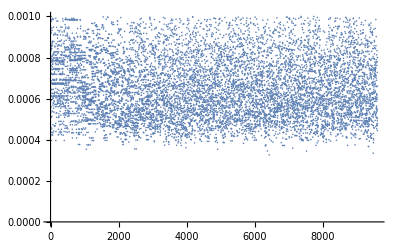

```mathematica
ListPlot[MixProd,PlotRange->All]
```

```mathematica
ii=1;Tabii={};While[ii≤ nFaces,If[MixProd[[ii]]< 0,AppendTo[Tabii,ii]];ii++];
```

```mathematica
Tabii
```

{}